```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<Segment.wl
```

```mathematica
<<Ocr.wl
```

```mathematica
ocrChinese@imageScaled[-Graphics-,5]
```

长久以来, 机器视觉认知一直是人们研究的热点, 它是研究使用机器或计算

```mathematica
plot:=ArrayPlot[#,ColorRules->{0->Blue,1->White,2->Red,3->Green},Mesh->All]&(*全黑会画成全白，坑了。用蓝代替黑*)
```

```mathematica
i=Import@"data/simple01.bmp"
```

-Graphics-

```mathematica
(*zhLines=i//segment//(#//splitByGreen//turnBlack/@#&//mergeSplitBy//Image[#,"Bit",Magnification->1]&//ColorNegate)&/@#&;*)
```

```mathematica
(*宽高比*)
ratioWidthHight[mts_]:=mts//Dimensions/@#&//(#[[1]]/#[[2]]&)/@#&
```

```mathematica
zhLines=i//imageLines//Take[#,5]&;
```

```mathematica
zhLines//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
zhLines//imageScaled[#,5]&/@#&//ocrChinese/@#&//TableForm
```

第四部分 预测试卷
预测试卷( 一一*)
一丹单项选择题(共70  1 分口 每题的备选项中,只有 1 个最
1. 下列关于法律规范的表述,错误的是( )口
A_ 法律规范是社会规范的一种

```mathematica
greenReds=zhLines//labelGreenRed/@#&;
```

```mathematica
(*greenRed=zhLines//First//labelGreenRed;*)
```

```mathematica
characters=greenRed//splitByGreenClean;
```

```mathematica
characterss=greenReds//splitByGreenClean/@#&;
```

```mathematica
characters=characterss//Flatten[#,1]&;
```

```mathematica
charactersImages=characters//Image[#,"Bit"]&/@#&;
```

```mathematica
ratio=characters//ratioWidthHight//FindClusters//Sort[#, Length[#1]>Length[#2]&]&//First
```

{77/74,77/64,77/75,77/76,77/74,77/73,1,1,59/58,59/60,59/58,59/58,59/60,43/37,43/39,43/40,43/40,43/40,43/40,43/41,43/19,43/20,43/41,43/40,43/41,43/41,43/40,43/40,43/36,43/40,43/40,43/39,43/34,43/36,43/39,43/41,43/40,43/41,43/41,43/85,43/40,43/39,43/42,43/39,43/40,43/41,43/41,43/39,43/37,43/41,43/40,43/41,43/40,43/37,43/41,20/17,1,1,40/41,1,40/41,40/41,40/41,40/41,40/39,10/9,1,40/39}

```mathematica
characters//ratioWidthHight
```

{77/74,77/64,77/75,77/76,77/74,77/73,1,1,59/58,59/60,59/58,59/58,59/17,59/60,59/18,43/37,43/13,43/39,43/40,43/40,43/40,43/40,43/11,43/41,43/19,43/20,43/41,43/7,43/40,43/41,43/12,43/41,43/12,43/40,43/40,43/36,43/40,43/40,43/39,43/34,43/7,43/36,43/39,43/12,43/41,43/40,43/41,43/41,43/85,43/11,43/12,43/6,43/40,43/39,43/42,43/39,43/40,43/41,43/41,43/39,43/37,43/41,43/40,43/7,43/41,43/40,43/37,43/41,43/11,43/12,43/13,20/17,1,1,40/41,1,40/41,40/41,40/41,40/41,40/39,10/9,1,40/39}

```mathematica
(*Quit[]*)
```

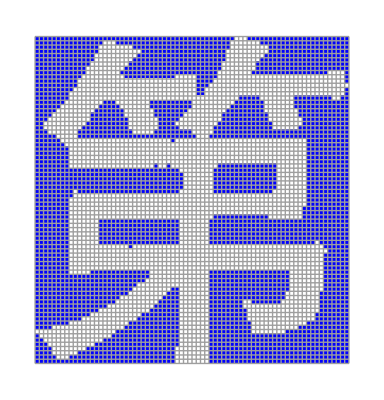
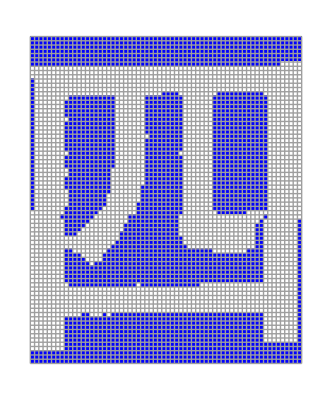
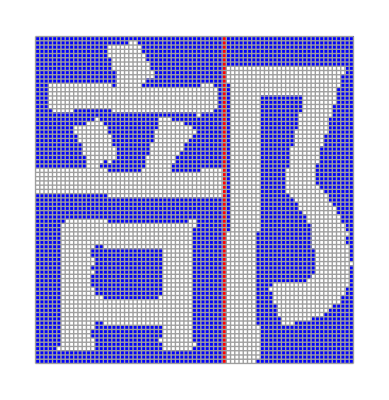
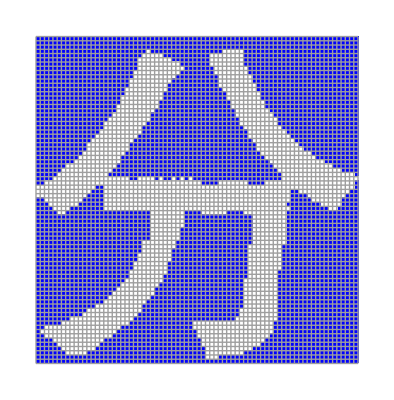
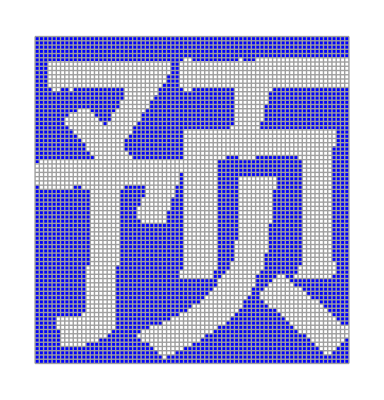
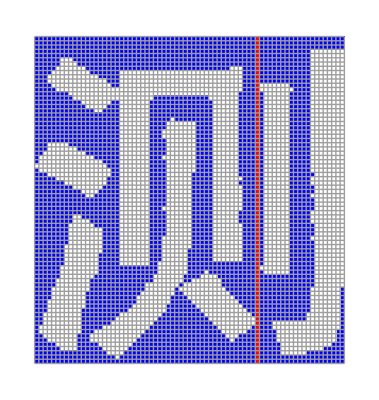
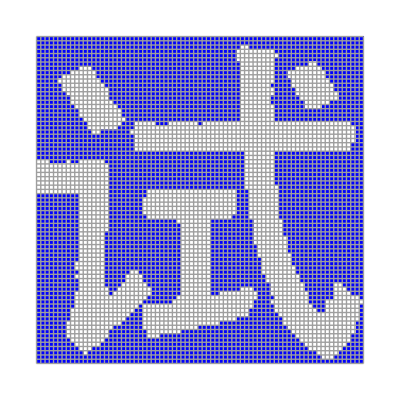
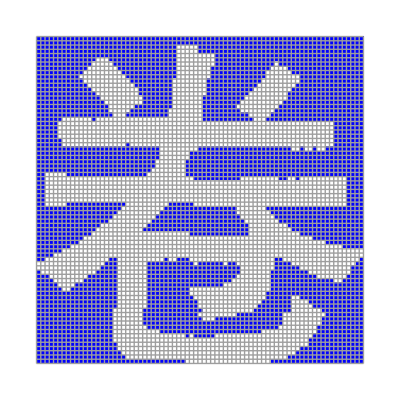

```mathematica
characters//plot/@#&
```

```mathematica
label[width_,height_]:=StringTemplate["w `1`,h `2`"][width, height]
```

```mathematica
showLabel[i_,label_]:=Show[i,Graphics[{Red,Text[label,{Center,Center},Background->Blue]}]]
```

```mathematica
charactersImages//showLabel[#,#//ImageData//Dimensions//label@@Reverse[#]&]&/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
charactersImages=characters//Image[#,"Bit"]&/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*所有字符的宽度*)
```

```mathematica
charactersWidths=charactersImages//ImageData/@#&//Dimensions/@#&//#[[2]]&/@#&
```

{74,64,75,76,74,73,77,77,58,60,58,58,17,60,18,37,13,39,40,40,40,40,11,41,19,20,41,7,40,41,12,41,12,40,40,36,40,40,39,34,7,36,39,12,41,40,41,41,85,11,12,6,40,39,42,39,40,41,41,39,37,41,40,7,41,40,37,41,11,12,13,34,40,40,41,40,41,41,41,41,39,36,40,39}

```mathematica
(*图片是否近似正方形，宽高比大于0.8 很可能是汉字*)
```

```mathematica
squareQ[i_]:=i//ImageData//Dimensions//#[[2]]/#[[1]]&//#>0.8&
```

```mathematica
charactersImages//showLabel[#,#//squareQ//ToString]&/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[charactersImages,squareQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}